```mathematica
νp=({{1, 1, 3}, {0, 0, 0}});
νr=({{0, 0, 2}, {0, 1, 1}});
S=(νp-νr);S//MatrixForm
```

(1 | 1 | 1
0 | -1 | -1)

```mathematica
MM = MatrixRank[S];
CL = Transpose@NullSpace[Transpose@S];
CC = NullSpace[S];
{NN,RR} = Dimensions[S];
λplusof[ρ_] :=SubPlus[k][ρ]Product[x[i]^νr[[i,ρ]],{i,1,NN}];λminusof[ρ_]:=SubMinus[k][ρ]Product[x[i]^νp[[i,ρ]],{i,1,NN}];
J =Table[λplusof[ρ]- λminusof[ρ],{ρ,1,RR}];
J //MatrixForm
```

(-x[1] k_-[1]+k_+[1]
-x[1] k_-[2]+x[2] k_+[2]
-x[1]^3 k_-[3]+x[1]^2 x[2] k_+[3])

```mathematica
A = S.J;A //MatrixForm
```

(-x[1] k_-[1]-x[1] k_-[2]-x[1]^3 k_-[3]+k_+[1]+x[2] k_+[2]+x[1]^2 x[2] k_+[3]
x[1] k_-[2]+x[1]^3 k_-[3]-x[2] k_+[2]-x[1]^2 x[2] k_+[3])

```mathematica
ss = Simplify@Solve[A == 0, Table[x[i],{i,1,NN}]][[1]]
```

{x[1]→(k_+[1])/(k_-[1]),x[2]→((k_-[1])^2 k_-[2] k_+[1]+k_-[3] (k_+[1])^3)/((k_-[1])^3 k_+[2]+k_-[1] (k_+[1])^2 k_+[3])}

```mathematica
Subscript[J, ss]= FullSimplify[J /.ss]
```

{0,((k_+[1])^3 (k_-[3] k_+[2]-k_-[2] k_+[3]))/((k_-[1])^3 k_+[2]+k_-[1] (k_+[1])^2 k_+[3]),((k_+[1])^3 (-k_-[3] k_+[2]+k_-[2] k_+[3]))/((k_-[1])^3 k_+[2]+k_-[1] (k_+[1])^2 k_+[3])}

```mathematica
Subscript[A, (1)] = FullSimplify[Grad[A,{x[1],x[2]}]/.ss]
```

{{-k_-[1]+k_-[2]-(k_-[3] (k_+[1])^2)/(k_-[1])^2-(2 ((k_-[1])^2 k_-[2]+k_-[3] (k_+[1])^2) k_+[2])/((k_-[1])^2 k_+[2]+(k_+[1])^2 k_+[3]),k_+[2]+((k_+[1])^2 k_+[3])/(k_-[1])^2},{k_-[2]+(3 k_-[3] (k_+[1])^2)/(k_-[1])^2-(2 (k_+[1])^2 ((k_-[1])^2 k_-[2]+k_-[3] (k_+[1])^2) k_+[3])/((k_-[1])^4 k_+[2]+(k_-[1])^2 (k_+[1])^2 k_+[3]),-k_+[2]-((k_+[1])^2 k_+[3])/(k_-[1])^2}}

```mathematica
rates = { SubPlus[k][1] -> 1,SubMinus[k][1]->1,SubPlus[k] [2] ->1, SubMinus[k][2]->α,SubPlus[k][3]->β,  SubMinus[k][3]->1}
```

{k_+[1]→1,k_-[1]→1,k_+[2]→1,k_-[2]→α,k_+[3]→β,k_-[3]→1}

```mathematica
T =FullSimplify[ Tr[Subscript[A, (1)]]]/.rates //Together
```

(-5-α-4 β+α β-β^2)/(1+β)

```mathematica
DD = FullSimplify[Det[Subscript[A, (1)]]]
```

k_-[1] k_+[2]+((k_+[1])^2 k_+[3])/(k_-[1])

```mathematica
Subscript[α, c] := (5 + 4β + β^2)/(β-1) (* β needs to be greater than 1 if we want α to be positive *)
```

```mathematica
T /. α ->  Subscript[α, c]//FullSimplify
```

0

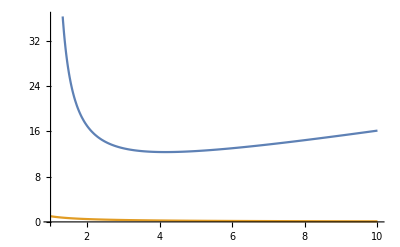

```mathematica
Plot[{(5 + 4β + β^2)/(β-1), 1/β},{β, 1, 10}]
```

```mathematica
Subscript[F, t] = A/. Table[x[i]->x[i][t],{i,1,NN}]/.rates
Subscript[α, c]/.β -> 3(* α needs to be greater than Subscript[α, c](β), fixed β, in order to have limit cycles *)
```

{1-x[1][t]-α x[1][t]-(x[1][t])^3+x[2][t]+β (x[1][t])^2 x[2][t],α x[1][t]+(x[1][t])^3-x[2][t]-β (x[1][t])^2 x[2][t]}

13

```mathematica
EQS=Table[D[x[i][t],t]==Subscript[F, t][[i]],{i,1,NN}]/.{α -> 13.00001,β ->3};EQS//MatrixForm
IC={x[1][0]==ss[[1]]+1,x[2][0]==ss[[2]]+1};
vars = Table[x[i][t],{i,1,NN}];
```

(x[1]'[t]==1-14. x[1][t]-(x[1][t])^3+x[2][t]+3 (x[1][t])^2 x[2][t]
x[2]'[t]==13. x[1][t]+(x[1][t])^3-x[2][t]-3 (x[1][t])^2 x[2][t])

```mathematica
Subscript[null, x][y1_]= (-1+(1+α)y1+y1^3)/(1+β y1^2)
```

(-1+y1^3+y1 (1+α))/(1+y1^2 β)

```mathematica
Subscript[null, y][y1_]=(α y1+y1^3)/(1+β y1^2)
```

(y1^3+y1 α)/(1+y1^2 β)

{x[1][t]→InterpolatingFunction[…][t],x[2][t]→InterpolatingFunction[…][t]}

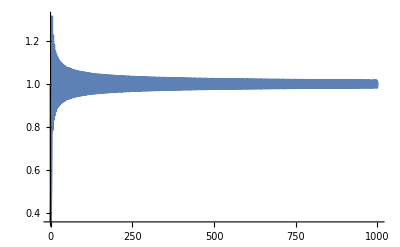

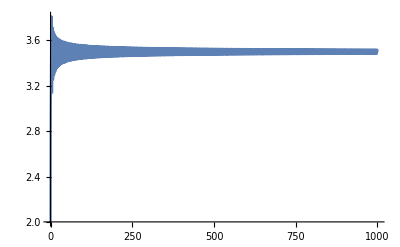

```mathematica
Subscript[t, max]=1000;
sols=NDSolve[{EQS,x[1][0] == 1, x[2][0] ==2},vars,{t,0,Subscript[t, max]}][[1]]
Plot[x[1][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
Plot[x[2][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
```

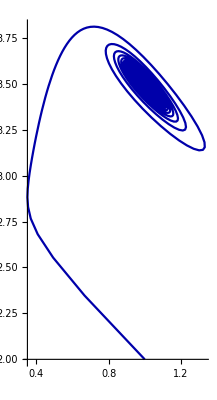

```mathematica
ParametricPlot[{x[1][t],x[2][t]}/.sols,{t,0,Subscript[t, max]},PlotRange->All,PlotPoints->200,PlotStyle->Darker@Blue]
```

```mathematica
$Assumptions = β >1
```

β>1

```mathematica
J /.ss /. rates /. α ->1/β//MatrixForm //FullSimplify (* The reversibility is given by α = 1/β *)
```

(0
0
0)

```mathematica
J /. rates //FullSimplify //MatrixForm
```

(1-x[1]
-α x[1]+x[2]
x[1]^2 (-x[1]+β x[2]))

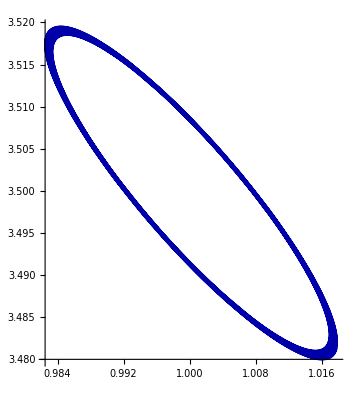

```mathematica
ParametricPlot[{x[1][t],x[2][t]}/.sols,{t,Subscript[t, max]*0.9,Subscript[t, max]},PlotRange->All,PlotPoints->500,PlotStyle->Darker@Blue]
```

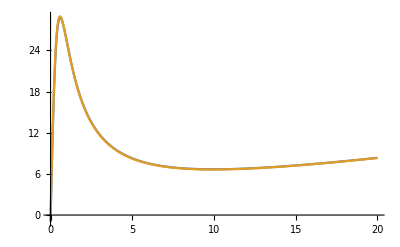

```mathematica
Plot[{Subscript[null, x][y1]/.{α -> 100,β ->3},Subscript[null, y][y1]/.{α -> 100,β ->3}},{y1,0,20},PlotRange->All]
```

```mathematica
$Assumptions = ϵ>0
```

ϵ>0

```mathematica
ss /.rates /. α -> Subscript[α, c]+ϵ //FullSimplify
```

{x[1]→1,x[2]→(4+β)/(-1+β)+ϵ/(1+β)}

```mathematica
Subscript[PA, (1)] = Subscript[A, (1)] /.rates //FullSimplify
```

{{-2+α-(2 (1+α))/(1+β),1+β},{(3+α+β-α β)/(1+β),-1-β}}

```mathematica
Collect[Subscript[PA, (1)],ϵ]
```

{{-2+α-(2 (1+α))/(1+β),1+β},{(3+α+β-α β)/(1+β),-1-β}}

```mathematica
Eigenvalues[Subscript[PA, (1)]/.ϵ->0 ]//FullSimplify
```

{-(5+α+4 β-α β+β^2+√(-4 (1+β)^3+(5+α-α β+β (4+β))^2))/(2 (1+β)),-(5+α+4 β-α β+β^2-√(-4 (1+β)^3+(5+α-α β+β (4+β))^2))/(2 (1+β))}

```mathematica
S.J/.ss /.rates /. α -> Subscript[α, c]+ϵ //FullSimplify
```

{0,0}

```mathematica
Clear[x]
vecx = Table[x[i],{i,1,NN}];
```

```mathematica
Subscript[PF, t] =Subscript[PA, (1)].(vecx-(vecx/.ss))/. Table[x[i]->x[i][t],{i,1,NN}]/.rates /.α -> Subscript[α, c]+ϵ //FullSimplify
```

{(-(1+β)^2 (3+2 β)-2 (-1+β) β ϵ+(-1+β) ((1+β)^2+(-1+β) ϵ) x[1][t]+(-1+β) (1+β)^2 x[2][t])/(-1+β^2),(2+2 β ((2+β)^2+(-1+β) ϵ)-(-1+β) (2-ϵ+β (3+β+ϵ)) x[1][t]-(-1+β) (1+β)^2 x[2][t])/(-1+β^2)}

```mathematica
solenoidal = Subscript[PF, t]/.ϵ ->0//FullSimplify
```

{((1+β) (-3-2 β+(-1+β) x[1][t]+(-1+β) x[2][t]))/(-1+β),(2+2 β (3+β)-(-2+β+β^2) x[1][t]-(-1+β^2) x[2][t])/(-1+β)}

```mathematica
PEQS=Table[D[x[i][t],t]==Subscript[PF, t][[i]],{i,1,NN}];PEQS//MatrixForm //FullSimplify
IC={x[1][0]==ss[[1]]+1,x[2][0]==ss[[2]]+1};
vars = Table[x[i][t],{i,1,NN}];
```

(x[1]'[t]==(-(1+β)^2 (3+2 β)-2 (-1+β) β ϵ+(-1+β) ((1+β)^2+(-1+β) ϵ) x[1][t]+(-1+β) (1+β)^2 x[2][t])/(-1+β^2)
x[2]'[t]==(2+2 β ((2+β)^2+(-1+β) ϵ)-(-1+β) (2-ϵ+β (3+β+ϵ)) x[1][t]-(-1+β) (1+β)^2 x[2][t])/(-1+β^2))

```mathematica
psols=DSolve[{PEQS,x[1][0] == x1, x[2][0] ==x2},vars,{t,0,Subscript[t, max]}][[1]]//FullSimplify
```

{x[1][t]→1+(ⅇ^((t (-1+β) ϵ)/(2 (1+β))) ((-1+x1) (-1+β) (4 (1+β)^3-(-1+β)^2 ϵ^2) Cosh[(t √(-4 (1+β)^3+(-1+β)^2 ϵ^2))/(2 (1+β))]-(2 (1+β)^2 (-3-x1-x2+(-2+x1+x2) β)+(-1+x1 (-1+β)-3 β) (-1+β) ϵ) √(-4 (1+β)^3+(-1+β)^2 ϵ^2) Sinh[(t √(-4 (1+β)^3+(-1+β)^2 ϵ^2))/(2 (1+β))]))/(4 (-1+β) (1+β)^3-(-1+β)^3 ϵ^2),x[2][t]→(ⅇ^(-(t ((-1+β) ϵ+√(-4 (1+β)^3+(-1+β)^2 ϵ^2)))/(2 (1+β))) (2 ⅇ^((t ((-1+β) ϵ+√(-4 (1+β)^3+(-1+β)^2 ϵ^2)))/(2 (1+β))) (4 (1+β)^3-(-1+β)^2 ϵ^2) (4-ϵ+β (5+β+ϵ))+ⅇ^((t (-1+β) ϵ)/(1+β)) (-4 β^5+β^4 (-32+(-4+ϵ) ϵ+4 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)-2 x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2))+β^3 (-88+20 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)-6 x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+ϵ (-8+ϵ (3+ϵ)+5 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)-2 x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)))+(-2+ϵ) (ϵ (2-ϵ+√(-4 (1+β)^3+(-1+β)^2 ϵ^2))-2 (-4+√(-4 (1+β)^3+(-1+β)^2 ϵ^2)+x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)))+β (-68+20 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+6 x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+ϵ (8-5 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+2 x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+ϵ (-3+3 ϵ-2 √(-4 (1+β)^3+(-1+β)^2 ϵ^2))))-x2 (-1+β^2) (-4 β^3+4 β (-3+√(-4 (1+β)^3+(-1+β)^2 ϵ^2))+β ϵ (-2 ϵ+√(-4 (1+β)^3+(-1+β)^2 ϵ^2))-(-2+ϵ) (-2-ϵ+√(-4 (1+β)^3+(-1+β)^2 ϵ^2))+β^2 (ϵ^2+2 (-6+√(-4 (1+β)^3+(-1+β)^2 ϵ^2))))+β^2 (-2 (56-16 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2))+ϵ (2 (2+x1) √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+ϵ (-5-3 ϵ+√(-4 (1+β)^3+(-1+β)^2 ϵ^2)))))+ⅇ^((t ((-1+β) ϵ+√(-4 (1+β)^3+(-1+β)^2 ϵ^2)))/(1+β)) (-4 β^5+β^4 ((-4+ϵ) ϵ+2 x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)-4 (8+√(-4 (1+β)^3+(-1+β)^2 ϵ^2)))-(-2+ϵ) (ϵ (-2+ϵ+√(-4 (1+β)^3+(-1+β)^2 ϵ^2))-2 (4+√(-4 (1+β)^3+(-1+β)^2 ϵ^2)+x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)))+β^3 (-88-20 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+6 x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+ϵ (-8+ϵ (3+ϵ)-5 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+2 x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)))+x2 (-1+β^2) (4 β^3+4 β (3+√(-4 (1+β)^3+(-1+β)^2 ϵ^2))-(-2+ϵ) (2+ϵ+√(-4 (1+β)^3+(-1+β)^2 ϵ^2))+β ϵ (2 ϵ+√(-4 (1+β)^3+(-1+β)^2 ϵ^2))+β^2 (-ϵ^2+2 (6+√(-4 (1+β)^3+(-1+β)^2 ϵ^2))))-β^2 (112+32 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)-2 x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+ϵ (2 (2+x1) √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+ϵ (5+3 ϵ+√(-4 (1+β)^3+(-1+β)^2 ϵ^2))))+β (-2 (34+10 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+3 x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2))+ϵ (8+5 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)-2 x1 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)+ϵ (-3+3 ϵ+2 √(-4 (1+β)^3+(-1+β)^2 ϵ^2)))))))/(2 (4 (-1+β) (1+β)^4-(-1+β)^3 (1+β) ϵ^2))}

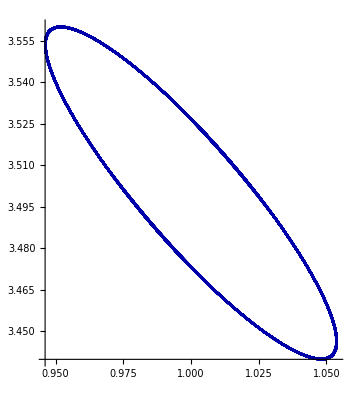

```mathematica
ParametricPlot[{x[1][t],x[2][t]}/.psols /.{β ->3,x1 ->1.05,x2->3.44,ϵ->0},{t,0,Subscript[t, max]},PlotRange->All,PlotPoints->200,PlotStyle->Darker@Blue]
```

```mathematica
Subscript[M, c]= Subscript[A, (1)] /.rates /. α->Subscript[α, c]//FullSimplify;Subscript[M, c]//MatrixForm
```

(1+β | 1+β
-2-β | -1-β)

```mathematica
vecδx[t_] = Table[δx[i][t],{i,1,NN}]
```

{δx[1][t],δx[2][t]}

```mathematica
Subscript[EQ, c]= D[vecδx[t],t] == Subscript[M, c].vecδx[t]
```

{δx[1]'[t],δx[2]'[t]}=={(1+β) δx[1][t]+(1+β) δx[2][t],(-2-β) δx[1][t]+(-1-β) δx[2][t]}

```mathematica
T = Transpose[Eigenvectors[Subscript[M, c]]]
U = Transpose[Eigenvectors[{{0,1},{-1,0}}]]
Q = Inverse[T].U //FullSimplify
```

{{-(1-√(-1-β)+β)/(2+β),-(1+√(-1-β)+β)/(2+β)},{1,1}}

{{-ⅈ,ⅈ},{1,1}}

{{((1-2 ⅈ)+√(-1-β)+(1-ⅈ) β)/(2 √(-1-β)),((1+2 ⅈ)+√(-1-β)+(1+ⅈ) β)/(2 √(-1-β))},{((-1+2 ⅈ)+√(-1-β)-(1-ⅈ) β)/(2 √(-1-β)),((-1-2 ⅈ)+√(-1-β)-(1+ⅈ) β)/(2 √(-1-β))}}

```mathematica
Subscript[yEQ, c]=Q.D[vecδx[t],t] ==Inverse[Q]. Subscript[M, c].Q.vecδx[t]//FullSimplify
```

{1/(4 √(-1-β) (2+β))(-ⅈ (2 √(-1-β)+(-3+2 √(-1-β)-2 β) β) δx[1][t]+((4+8 ⅈ)+(4-2 ⅈ) √(-1-β)+β ((6+11 ⅈ)+(2-2 ⅈ) √(-1-β)+(2+4 ⅈ) β)) δx[2][t]+2 (2+β) (((1-2 ⅈ)+√(-1-β)+(1-ⅈ) β) δx[1]'[t]+((1+2 ⅈ)+√(-1-β)+(1+ⅈ) β) δx[2]'[t])),1/(4 √(-1-β) (2+β))(((4+2 ⅈ) (-2 ⅈ+√(-1-β))+β ((6-11 ⅈ)+(2+2 ⅈ) √(-1-β)+(2-4 ⅈ) β)) δx[1][t]+ⅈ (2 √(-1-β)+(-3+2 √(-1-β)-2 β) β) δx[2][t]+2 (2+β) (((-1+2 ⅈ)+√(-1-β)-(1-ⅈ) β) δx[1]'[t]+((-1-2 ⅈ)+√(-1-β)-(1+ⅈ) β) δx[2]'[t]))}=={0,0}

```mathematica
vecss = Table[x[i],{i,1,NN}]
```

{x[1],x[2]}

```mathematica
SubStar[x]= vecss /.ss/.rates
```

{1,(1+α)/(1+β)}